```mathematica
(* upload of a picture *)
img=-Graphics-;
```

```mathematica
(* application of contrast-preserving bleaching *)
imgGrayscale=ImageEffect[img,"Decolorization"]
```

```mathematica
(* Convert the image to an array of pixel values *)
ImageData[imgGrayscale][[{1,2}]];
ImageData[img][[{1,2}]];
(* Convert the array of pixel values to an image *)
ArrayPlot[ImageData[imgGrayscale],ColorFunction->GrayLevel]
```

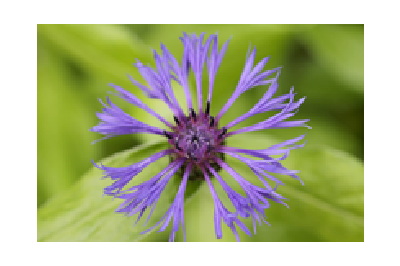
```mathematica
(* Decomposition into three RGB channels *)
cimg=-Graphics-;
GraphicsRow[Prepend[MapThread[ArrayPlot[ImageData[#1],ColorFunction->#2]&,{ColorSeparate[cimg],{RGBColor[#,0,0]&,RGBColor[0,#,0]&,RGBColor[0,0,#]&}}],cimg]]
```

```mathematica
(* Graphic representation of an image using a histogram *)
GraphicsRow[{img,ImageHistogram[img,FrameTicks->{Automatic,None},AspectRatio->1]}]
GraphicsRow[{imgGrayscale,ImageHistogram[imgGrayscale,FrameTicks->{Automatic,None},AspectRatio->1]}]
```